# Algorytm

## Wczytanie danych

```mathematica
allFilesPD04n1000 =FileNames["PD_4_1000*.csv","./data"]
```

{./data/PD_4_1000_01.csv,./data/PD_4_1000_02.csv,./data/PD_4_1000_03.csv,./data/PD_4_1000_04.csv,./data/PD_4_1000_05.csv,./data/PD_4_1000_06.csv,./data/PD_4_1000_07.csv,./data/PD_4_1000_08.csv,./data/PD_4_1000_09.csv,./data/PD_4_1000_10.csv,./data/PD_4_1000_11.csv,./data/PD_4_1000_12.csv,./data/PD_4_1000_13.csv,./data/PD_4_1000_14.csv,./data/PD_4_1000_15.csv,./data/PD_4_1000_16.csv,./data/PD_4_1000_17.csv,./data/PD_4_1000_18.csv,./data/PD_4_1000_19.csv,./data/PD_4_1000_20.csv}

```mathematica
allFilesPD04n2000 =FileNames["PD_4_2000*.csv","./data"]
```

{./data/PD_4_2000_01.csv,./data/PD_4_2000_02.csv,./data/PD_4_2000_03.csv,./data/PD_4_2000_04.csv,./data/PD_4_2000_05.csv,./data/PD_4_2000_06.csv,./data/PD_4_2000_07.csv,./data/PD_4_2000_08.csv,./data/PD_4_2000_09.csv,./data/PD_4_2000_10.csv,./data/PD_4_2000_11.csv,./data/PD_4_2000_12.csv,./data/PD_4_2000_13.csv,./data/PD_4_2000_14.csv,./data/PD_4_2000_15.csv,./data/PD_4_2000_16.csv,./data/PD_4_2000_17.csv,./data/PD_4_2000_18.csv,./data/PD_4_2000_19.csv,./data/PD_4_2000_20.csv}

```mathematica
allFilesPD08n1000 =FileNames["PD_8_1000*.csv","./data"]
```

{./data/PD_8_1000_01.csv,./data/PD_8_1000_02.csv,./data/PD_8_1000_03.csv,./data/PD_8_1000_04.csv,./data/PD_8_1000_05.csv,./data/PD_8_1000_06.csv,./data/PD_8_1000_07.csv,./data/PD_8_1000_08.csv,./data/PD_8_1000_09.csv,./data/PD_8_1000_10.csv,./data/PD_8_1000_11.csv,./data/PD_8_1000_12.csv,./data/PD_8_1000_13.csv,./data/PD_8_1000_14.csv,./data/PD_8_1000_15.csv,./data/PD_8_1000_16.csv,./data/PD_8_1000_17.csv,./data/PD_8_1000_18.csv,./data/PD_8_1000_19.csv,./data/PD_8_1000_20.csv}

```mathematica
allFilesPD16n1000 =FileNames["PD_16_1000*.csv","./data"]
```

{./data/PD_16_1000_01.csv,./data/PD_16_1000_02.csv,./data/PD_16_1000_03.csv,./data/PD_16_1000_04.csv,./data/PD_16_1000_05.csv,./data/PD_16_1000_06.csv,./data/PD_16_1000_07.csv,./data/PD_16_1000_08.csv,./data/PD_16_1000_09.csv,./data/PD_16_1000_10.csv,./data/PD_16_1000_11.csv,./data/PD_16_1000_12.csv,./data/PD_16_1000_13.csv,./data/PD_16_1000_14.csv,./data/PD_16_1000_15.csv,./data/PD_16_1000_16.csv,./data/PD_16_1000_17.csv,./data/PD_16_1000_18.csv,./data/PD_16_1000_19.csv,./data/PD_16_1000_20.csv}

## Proste wykresy

```mathematica
makePlot[s_]:=ListLinePlot[Rest@Import[s],PlotRange->{0,1},PlotLabel->s]
```

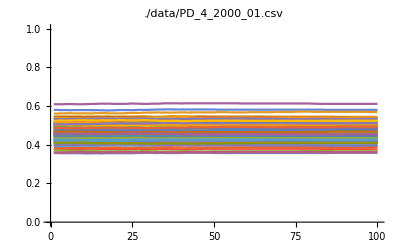
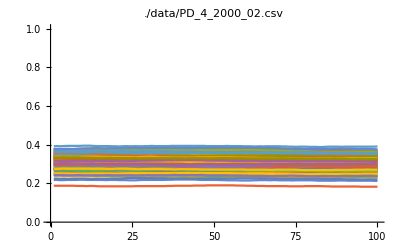
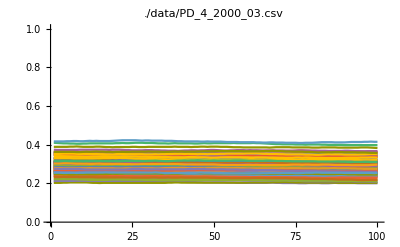
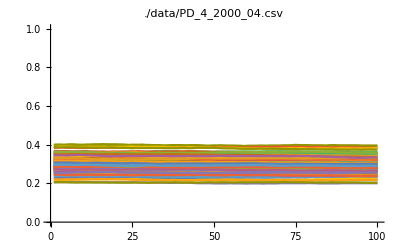
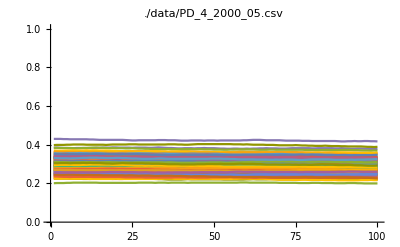
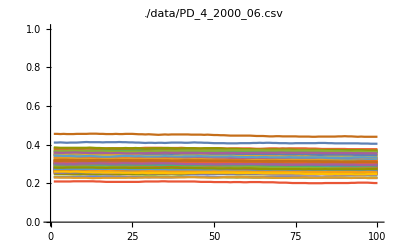
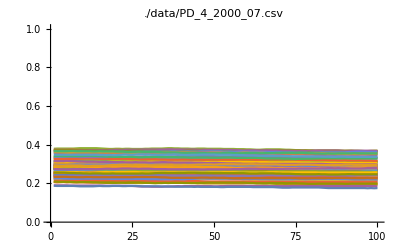
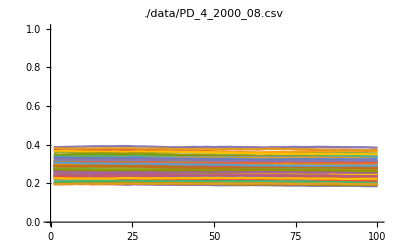

```mathematica
makePlot/@allFilesPD04n1000
```

## Testowanie czy liczba kroków coś zmienia

```mathematica
makeMean[s_]:=Mean[Flatten@Rest@Import[s]]
```

```mathematica
updateMakeMean[v_]:=Transpose[{Range[1,1.95,0.05],makeMean/@v}]
```

```mathematica
fig1=ListLinePlot[updateMakeMean[allFilesPD04n1000],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1, GridLines->{{1.5},Automatic},PlotStyle->Blue];
```

```mathematica
fig2=ListLinePlot[updateMakeMean[allFilesPD04n2000],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1, GridLines->{{1.5},Automatic},PlotStyle->Orange];
```

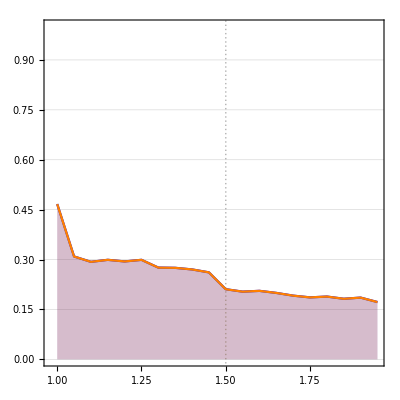

```mathematica
Show[fig1, fig2]
```

## Sprawdzanie profile dla różnych grafów

```mathematica
makeMean[s_]:=Mean[Flatten@Rest@Import[s]]
```

```mathematica
updateMakeMean[v_]:=Transpose[{Range[1,1.95,0.05],makeMean/@v}]
```

```mathematica
fig1=ListLinePlot[Callout[updateMakeMean[allFilesPD04n1000],"4"],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1, GridLines->{{1.5},Automatic},PlotStyle->Blue];
```

```mathematica
fig2=ListLinePlot[Callout[updateMakeMean[allFilesPD08n1000],8],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1, GridLines->{{1.5},Automatic},PlotStyle->Orange];
```

```mathematica
fig3=ListLinePlot[Callout[updateMakeMean[allFilesPD16n1000],16],Filling->Axis,PlotRange->{0,1},Frame->True,PlotTheme->"Detailed",AspectRatio->1, GridLines->{{1.5},Automatic},PlotStyle->Cyan];
```

```mathematica
Show[fig1, fig2,fig3]
```

-Graphics-

## Init

```mathematica
SetDirectory[NotebookDirectory[]];
```